```mathematica
Manipulate[
Module[{t,S,L,w,Lc,r1,r2,r2c,Ac,P,h,Tb,k,m,qf,T,base,rectangular,annular,temperature,col},
(*size stuff*)
t=0.0015;(*m*)
S=0.01;

(*rectangular*)
L:=length/1000;
w:=width/1000;
Lc:=L+t/2;

(*annular*)
r1=0.003;(*base radius*)
r2:=radius2/1000;(*fin radius*)
r2c:=r2+t/2;

If[fin==1,
{Ac:=2*w*Lc;P:=2*w+2*t;},
{Ac:=2*π*(r2c^2-r1^2);P:=4*π*r2c;}];

(*therm. data*)
h=35;(*W/m2/K*)
Tb=500;(*base temp.*)
k:=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401,(*copper*)
mat==7,2300(*diamond*)
];(*W/m/K*)

m:=√((2*h)/(k*t));
qf[z_]:=Tb*√(h*P*k*Ac)*Tanh[m*z];
T[z_,x_]:=Tb*Cosh[m*(z-x)]/Cosh[m*z];

base=-0.005;

col[z_,Tmin_,x_]:=ColorData["TemperatureMap"][Rescale[T[z,x],{Tmin,500}]];
(*col[x_]:=ColorData["TemperatureMap"][Rescale[T[L,x],{286.7,500}]];*)

rectangular:=Show[
Graphics3D[{GrayLevel[0.5],Cuboid[{base,0,0},{0,w,2*S+t}]}],
RegionPlot3D[z<S+t,{x,0,L},{y,0,w},{z,S,S+t},Mesh->None,
ColorFunction->(col[L,286.7,#1]&),ColorFunctionScaling->False]
];

annular:=Show[
Graphics3D[{GrayLevel[0.5],Cylinder[{{0,0,0},{0,0,2*S+t}},r1]}],
ParametricPlot3D[{u*Sin[θ],u*Cos[θ],S+t},{u,r1,r2},{θ,0,2*π},Mesh->None,ColorFunction->(col[r2,357.4,#1]&),ColorFunctionScaling->False]
];

(*temperature:=If[fin==1,
Plot3D[T[L,x],{x,0,L},{y,0,w},Mesh->None,ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[z,{286.7,500}]]],ColorFunctionScaling->False],
Plot3D[T[r2,x],{x,0,r2},{y,0,r2},Mesh->None,ColorFunction->Function[{x,y,z},ColorData["TemperatureMap"][Rescale[z,{357.4,500}]]],ColorFunctionScaling->False]
];*)

Show[Switch[fin,1,rectangular,2,annular],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{250,350}]

],
Column[{
Control[{{fin,1,""},{1->" rectangular ",2->" annular "},Setter}],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper",7->"diamond"},PopupMenu}],
Style["fin measurements (mm)",Bold],
PaneSelector[{
1->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}],
2->Control[{{radius2,10,"radius"},5,15,1,Appearance->"Labeled",ImageSize->Small}],
3->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}]
},Dynamic@fin]
}]
]
```

```mathematica
ParametricPlot3D[{u*Sin[t],u*Cos[t],0.},{u,0.5,1},{t,0,2*π},Mesh->None,ColorFunction->(ColorData["Rainbow"][#4]&)]
```

-Graphics3D-

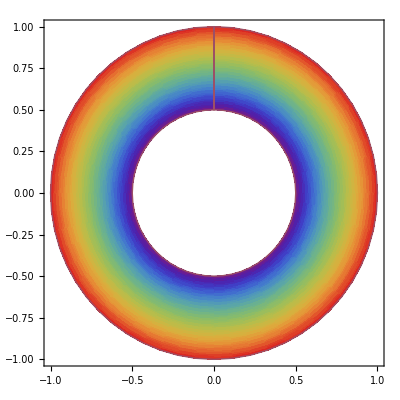

```mathematica
ParametricPlot[{u*Sin[t],u*Cos[t]},{u,0.5,1},{t,0,2*π},ColorFunction->(ColorData["Rainbow"][#3]&)]
```

```mathematica
ParametricPlot[{u*Sin[t],u*Cos[t]},{u,0.5,1},{t,0,2*π},ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z]]]
```

-Graphics-

```mathematica
RegionPlot3D[x^2+y^2<2,{x,-2,2},{y,-2,2},{z,0,2},
Mesh->None,
ColorFunction->(ColorData["Rainbow"][#3]&)
]
```

-Graphics3D-